```mathematica
list = {{{0.,0.},{.5,N[Sqrt[3/4]]},{1.,0.}}};
```

```mathematica
triple[d_]:=Block[{d1,d2,d3},
d1 = {d[[1]],(d[[2]]+d[[1]])*.5,
(d[[3]]+d[[1]])*.5};
d2=d1+Table[(d1[[3]]-d1[[1]]),{3}];
d3=d1+Table[(d1[[2]]-d1[[1]]),{3}];
{d1,d2,d3}]
```

```mathematica
plot1:=Block[{listtwo,plotlist},
listtwo=Map[triple,list];
list=Flatten[listtwo,1];
plotlist=Map[Polygon,list];
Show[Graphics[plotlist],
AspectRatio->Automatic]]
```

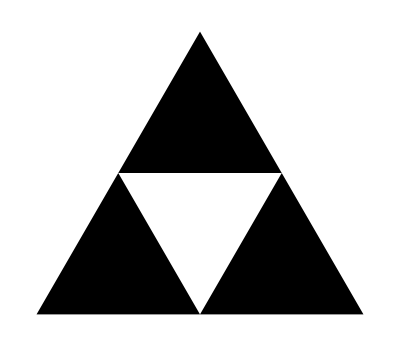

```mathematica
plot1
```